# -Graphics-

# Wolfram Language for Python Users

## Creating a Unified Workflow

```mathematica
Image[Import[FileNameJoin[{"Images", "MathematicaLogo.png"}]], ImageSize -> 250]
```

-Graphics-

## Contents

Introduction

Brief history

Broad Comparison

Similarities

Differences

Code structure

Out-of-the-box functionality

Functions for everything

Curated data

Examples

Calculus

Core language

Functional programming

Data analysis

Python in Wolfram Language environments

Connecting to Python

Wolfram Language in Python environments

Connecting to Mathematica

Final look

Unique applications

Wolfram resources

Cloud deployment

Summary

References

## Introduction

### Key Questions

How does Wolfram Language stack up to Python?

Functionality

Usability

Interface

What is transferable between Python and Wolfram Language?

Code

Data types

Experience

What are the best practices for a combined experience?

Development

Deployment

## Brief History

### Python

```mathematica
Image[Import[FileNameJoin[{"Images", "PythonLogo.png"}]], ImageSize -> 150]
```

-Graphics-

First published in 1991 as a successor to ABC (see history)

Current: V3.11.1 (December 2022)

Object-oriented language that emphasises readability

The first Python notebooks appeared in IPython (2001), inspired by Mathematica notebooks

### Mathematica

```mathematica
Image[Import[FileNameJoin[{"Images", "WolframLogo.png"}]], ImageSize -> 150]
```

-Graphics-

First released in 1988 (see release history)

Current: V13.2 (December 2022)

A combined kernel (Wolfram Language) and front-end notebook (Mathematica) interface

Symbolic computation

Emphasises computation and automation; allows for arbitrary structures and data

#### Side note: Mathematica vs. Wolfram Language

```mathematica
Grid[
{
MapThread[
Hyperlink[
Column[
{
Import[FileNameJoin[{"Images", #1}]],
#2
},
Alignment -> Center,
Spacings -> 1
],
#3
]&,
{
{"MathematicaLogo.png", "WolframLogo.png"},
{"Mathematica", "Wolfram Language"},
{"https://www.wolfram.com/mathematica/", "https://www.wolfram.com/language/"}
}
]
},
Alignment -> Bottom,
BaseStyle -> "Text",
Spacings -> {3, Automatic}
]
```

[-Graphics-
Mathematica](https://www.wolfram.com/mathematica/) | [-Graphics-
Wolfram Language](https://www.wolfram.com/language/)

While initially conceived together, Mathematica and Wolfram Language (WL) are now considered separate entities. Mathematica is an interactive notebook IDE for Wolfram Language that allows output to be displayed directly with input code. Inputs and outputs are contained in "cells" which are paired together and can be moved/copied together or separately. Many other cells types are available: text, section, item, natural language… and many more.

Mathematica is not the only IDE which supports Wolfram Language:

```mathematica
Grid[
{
MapThread[
Hyperlink[
Column[
{
Import[FileNameJoin[{"Images", #1}]],
#2
},
Alignment -> Center,
Spacings -> 1
],
#3
]&,
{
{"VSCodeLogo.png", "IntelliJLogo.png", "EclipseLogo.png"},
{"VSCode", "IntelliJ", "Eclipse"},
{"https://code.visualstudio.com/", "https://www.jetbrains.com/idea/", "https://eclipseide.org/release/"}
}
]
},
Alignment -> Bottom,
BaseStyle -> "Text",
Spacings -> {3, Automatic}
]
```

[-Graphics-
VSCode](https://code.visualstudio.com/) | [-Graphics-
IntelliJ](https://www.jetbrains.com/idea/) | [-Graphics-
Eclipse](https://eclipseide.org/release/)

In addition to Mathematica notebooks, Wolfram Language can be written in code-only Wolfram Language files, “paclets” (collections of files), command-line scripts (WolframScript) or on the web (Wolfram Cloud).

## Broad Comparison

### Similarities

Both Python and Wolfram Language:

are low-preamble interactive languages

focus on computation and support science and mathematical concepts

support a number of IDEs (VSCode, IntelliJ, Eclipse, shell, scripts, notebook)

are considered multi-paradigm, high-level languages

allow for code delivery in multiple forms

do not require memory management or compilation for most applications

### Differences

#### Python

An open-source language developed by members of the community

Free to use but a number of implementations and dialects

Some functionality is not forwards/backwards compatible with major releases

Ships with minimal primitives, and relies on externally developed packages

#### Wolfram Language

A single-source language, developed in-house at Wolfram Research

Proprietary licence but consistent, centralised maintenance of language and documentation

Virtually all internal functions are backwards compatible

A great deal of functionality is provided out of the box:

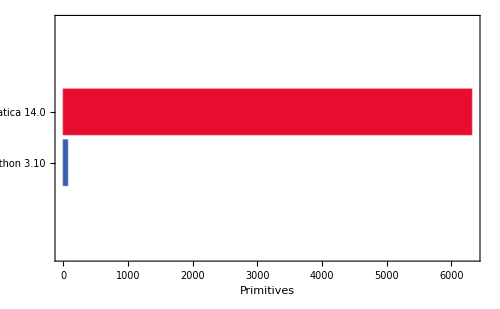

```mathematica
CellPrint[
ExpressionCell[
With[
{
pythonFunctions={"abs","aiter","all","any","anext","ascii","bin","bool","breakpoint","bytearray","bytes","callable","chr","classmethod","compile","complex","delattr","dict","dir","divmod","enumerate","eval","exec","filter","float","format","frozenset","getattr","globals","hasattr","hash","help","hex","id","input","int","isinstance","issubclass","iter","len","list","locals","map","max","memoryview","min","next","object","oct","open","ord","pow","print","property","range","repr","reversed","round","set","setattr","slice","sorted","staticmethod","str","sum","super","tuple","type","vars","zip","__import__"}
(* Source: https://docs.python.org/3/library/functions.html#breakpoint *)
},
BarChart[
{Length[pythonFunctions],Length[EntityList["WolframLanguageSymbol"]]},
ChartLabels->{"Python 3.10","Mathematica 14.0"},
ChartStyle->{RGBColor[0.23,0.37,0.67], RGBColor[0.9,0.05,0.18]},
BarOrigin->Left,
Frame -> {{True, False}, {True, False}},
FrameLabel -> {None, "Primitives"},
ImageSize -> 500,
BaseStyle -> 14
]
],
"Output",
GeneratedCell -> False
]
]
```

### Code Structure

#### Syntax

Brackets and commas in Wolfram Language are indentations in Python.

Square brackets in Wolfram Language are parentheses in Python.

Comments are bracketed (* *) in Wolfram Language but delimited with # in Python.

Wolfram Language will print all intermediary results and assignments by default, while Python will not.

Indices start at 1 in Wolfram Language, but 0 in Python.

Whitespace does not matter in Wolfram Language*, but does in Python.

*A space character can be used as multiplication in algebraic computation.

#### Example: Determine whether a number is prime

Writing Wolfram Language code in the style of Python is often possible…

Python | Wolfram Language
  |  
number=417

# prime numbers are greater than 1
if number>1:
	for i in range(2,number):
		if (number % i)==0:
			print(number,"is not prime")
			print("factors:",i,"&",number//i)
			break
		if i==(number-1):
			print(number,"is prime")

else:
	print(number,"is not prime")
number=417

# prime numbers are greater than 1
if number>1:
   for i in range(2,number):
       if (number % i)==0:
           print(number,"is not prime")
            print("factors:",i,"&",number//i)
            break
        if i==(number-1):
           print(number,"is prime")

else:
   print(number,"is not prime") | number = 417;

(*prime numbers are greater than 1*)
If[number > 1,
	For[i=2,i<number,i++,
		If[ Mod[number, i] ==0,
			Print[number, " is not prime"];
			Print["factors: ",i," & ",number/i];
			Break[];
		];
		If[i==number-1,
			Print[number," is prime"]]
		],
Print[number," is not prime"]
]

…but alternative approaches are also possible:

```mathematica
Clear[primeCheck];

primeCheck[number:1]:=StringForm["`1` is not Prime",number];

primeCheck[number_]:= Block[
{i=2},
While[Mod[number,i]≠0&&i<number,i++];
If[
i==number,
StringForm["`1` is Prime",number],
StringForm["`1` is not Prime, factors: `2`, `3`",number, i, number/i]
]
];
```

```mathematica
primeCheck[1]
primeCheck[7]
primeCheck[10]
```

## Out-of-the-Box Functionality

### Functions for… Everything

See the cumulative numbers of Wolfram Language symbols introduced in successive major versions of Mathematica:

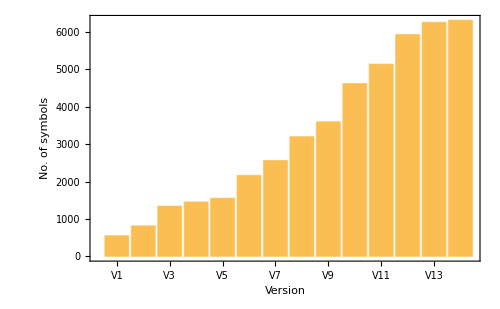

```mathematica
BarChart[
Once[Accumulate[Sort[Tally[Round[EntityValue["WolframLanguageSymbol","VersionIntroduced"]]]][[All,-1]]]],
ChartLabels->{"V1","V2","V3","V4","V5","V6","V7","V8","V9","V10","V11","V12","V13","V14"},Frame->{{True,False},{True,False}},FrameLabel->{"Version","No. of symbols"},ImageSize->500
]
```

With so many built-in functions, there’s a good chance the hard work has been done for you:

```mathematica
prime=921407;

PrimeQ[prime]
```

Built-in functions are virtually always quicker than user-made functions:

```mathematica
primeCheck[prime]//RepeatedTiming
```

```mathematica
PrimeQ[prime]//RepeatedTiming
```

The documentation lists similar functions for quick development of ideas:

```mathematica
PrimeQ[10^50+3]
```

```mathematica
FactorInteger[10^50+3]
```

### Curated Data

Wolfram Language is connected to the Wolfram Knowledgebase: a vast repository of computable knowledge that powers Wolfram|Alpha.

Get knowledge on maths, science & technology, society & culture and everyday life:

discontinuities (x^3+8)/(x^3+3x^2-4x-12)

carbon steel

flintstones vs the simpsons

second cousin once removed

Get knowledge on the language itself:

Graphics function version history

```mathematica
Information[RandomChoice[WolframLanguageData[]]]
```

## Examples

### Calculus

#### Example: Integration

Find the indefinite integral ∫ ⅇ^x Cos[x]+5x y Cos[y]ⅆx and plot its curve.

##### Python

In Python, symbolic integration and plotting require separate imports:

# sympy for symbolic integration

from sympy import *
x, y = symbols('x y')
ans = integrate(exp(x) * cos(x) + 5*x*y*cos(y), x)
print(ans)


# numpy and scipy for numerical methods

import matplotlib as mpl
from mpl_toolkits.mplot3d import Axes3D
import numpy as np
import matplotlib.pyplot as plt

def f(x, y):
	return 5 * x ** 2 * y * np.cos(y)/2 + np.exp(x) * np.sin(x)/2 + np.exp(x) * np.cos(x)/2

x = np.linspace(-1, 1, 10)
y = np.linspace(-10, 10, 100)

X, Y = np.meshgrid(x, y)
Z = f(X, Y)

fig = plt.figure()
ax = plt.axes(projection='3d')
#ax.contour3D(X, Y, Z, 50, cmap='binary')
#ax.plot_wireframe(X, Y, Z, color='orange')
ax.plot_surface(X, Y, Z, rstride=1, cstride=1, cmap='Oranges', edgecolor='none')


plt.show()

##### Wolfram Language

In Wolfram Language, computation is unified:

```mathematica
ans = Integrate[ⅇ^x*Cos[x] + 5x y Cos[y],x]
```

```mathematica
Plot3D[ans,{x, -1,1},{y, -10,10},PlotRange->All, SphericalRegion->True]
```

### Core Language

#### Example: Letter counts

Find the number of letters across several words and find their product.

##### Python

In Python, anonymous functions are made with lambda functions and primitives are limited to a few data types:

from functools import reduce

result = list(map(len, ('Red', 'Blue', 'Green'))) #get letter counts for each word
print(result)

reduce(lambda x, y: x*y, result) #get the product of the result

##### Wolfram Language

In Wolfram Language, anonymous functions use Function:

```mathematica
result = Map[Function[str, StringLength[str]], {"Red","Blue","Green"}]

Apply[Times,result]
```

Due to the symbolic nature of the language, inputs can often be arbitrary:

```mathematica
Apply[Times,{-Graphics-,-Graphics-}]
```

### Functional Programming

Guide: Functional Programming

#### Example: User-made functions

Define a function f such that f(x,c) = Piecewise[{{√x+ c,, x>0 and x even}, {√x- c,, x>0 and x odd}, {Fail,, x≤ 0}}].

##### Python

In Python, branching functions are common:

import math

def myFunc1(x, c):
	if (x > 0) & (x % 2) == 0:
		return math.sqrt(x) + c
	elif x > 0:
		return math.sqrt(x) - c
	else:
		raise ValueError("The argument ", x, " is not greater than or equal to zero.")

print(myFunc1(4, 2))
print(myFunc1(1, 2))
print(myFunc1(-1, 2))

##### Wolfram Language

In Wolfram Language, overloading with extensive pattern matching is more common:

```mathematica
Clear[myFunc1]

myFunc1[x_?(EvenQ[#]&&#>0&),c_]:=Sqrt[x]+c;
myFunc1[x_?(OddQ[#]&&#>0&),c_]:=Sqrt[x]-c;
myFunc1[x_,c_]:=Message[myFunc1::nnarg,x];

myFunc1::nnarg="The argument `1` is not greater than or equal to zero.";
```

```mathematica
myFunc1[4,2]
myFunc1[1,2]
myFunc1[-1,2]
```

### Data Analysis

#### Example: Classifier

Produce a simple classifier based on a multivariate dataset that returns survival probabilities.

##### Python

In Python, machine learning requires prior knowledge (e.g. logistic regression):

import pandas as pd
import numpy as np
import os
import csv
from sklearn.linear_model import LogisticRegression


# import data 
os.chdir('<file path>') # Replace <file path> with the path of the folder containing the CSV file
data = pd.read_csv('titanic.csv', header = 0)
data = data.dropna() #drop n.a


print(data.head())
print('--------------------------------------------')

# create dummy variables for nominals
cat_vars = ['Class', 'Gender', 'Outcome']
for var in cat_vars:
    cat_list = 'var'+'_'+var
    cat_list = pd.get_dummies(data[var], prefix=var, drop_first=True)
    data1 = data.join(cat_list)
    data = data1

data_vars = data.columns.values.tolist()
to_keep = [i for i in data_vars if i not in cat_vars]
data_final = data[to_keep]


print(data_final.head())
print('--------------------------------------------')

# partition
X = data_final.loc[:, data_final.columns != 'Outcome_survived']
y = data_final.loc[:, data_final.columns == 'Outcome_survived']

clf = LogisticRegression(random_state = 0).fit(X, y.values.ravel())
print(clf.predict([[23., 0., 1., 1.]]))
print(clf.predict_proba([[23., 0., 1., 1.]]))

##### Wolfram Language

In Wolfram Language, machine learning workflows are clean and largely automated.

Get some data on the Titanic:

```mathematica
tData = Import["titanic.csv",{"CSV", "Dataset"},"HeaderLines"->1]
```

Train a classifier on the data:

```mathematica
titanic=Classify[tData -> "Outcome"]
```

```mathematica
(*titanic=Classify[tData -> "Outcome", Method -> "DecisionTree"]*)
```

Use the classifier to make predictions:

```mathematica
titanic[<|"Class" -> "3rd","Age" -> 23,"Gender" -> "male"|>,"Probabilities"]
```

```mathematica
Information[titanic]
```

## Python in WL Environments

### Connecting to Python

#### External evaluation cells

Use specialised cells to write Python directly in a Mathematica notebook:

list = range(10)
list

Alternatively, use ExternalEvaluate:

```mathematica
numpyArray = ExternalEvaluate["Python","
import numpy as np
list = np.arange(10)
list
"]//Normal
```

The benefit of using ExternalEvaluate is that Wolfram Language can be injected:

```mathematica
ExternalEvaluate["Python","
import numpy as np
list = np.arange("<>ToString[10]<>")
list
"]//Normal
```

#### Working with external evaluation cells

Definitions carry across multiple ExternalEvaluate cells, providing the session has not been terminated in between:

list

```mathematica
Quit
```

list

#### Transferring data

ExternalEvaluate allows data to be passed between Python instances and Wolfram Language:

```mathematica
numpyIntArray=ExternalEvaluate["Python","
import numpy as np
x = np.arange(60)
y=x.reshape(3,4,5)
y
"];
```

```mathematica
Normal[numpyIntArray]
```

Python-specific data types (.npy or .npz) can be imported directly:

```mathematica
numpyIntArray2=ExternalEvaluate["Python",{
"import numpy as np",
"import os",
"os.chdir('"<>NotebookDirectory[]<>"')",
"os.getcwd()",
"np.save('1to6', np.array([[1, 2, 3], [4, 5, 6]]))",
"np.load('1to6.npy')"
}
];

Normal[Last[numpyIntArray2]]
```

## WL in Python Environments

### Connecting to Mathematica

#### Wolfram Client Library

Utilising Wolfram Language within Python requires the Wolfram Client Library for Python. (This requires Python 3.5 or higher and Wolfram Language 11.3 or higher. It can be installed using pip or by cloning the Git repository.)

The client library allows Python to:

Evaluate any Wolfram Language expression

Access any of Wolfram Language’s 6000+ predefined functions

Access the Wolfram Knowledgebase

Utilise Wolfram|Alpha's natural language processing

Construct expressions to be evaluated once they enter a Wolfram environment

#### Python environment

Let’s move to a Python environment in four Jupyter notebooks:

```mathematica
CellPrint[
ExpressionCell[
Column[
MapThread[
Button[
Mouseover[#1, Style[#1, FontColor -> RGBColor[1,0.6,0.1]]],
If[
FailureQ[
SystemOpen[
FileNameJoin[{
NotebookDirectory[],
#2<>".ipynb"
}]
]
],
SystemDialogInput["FileOpen"]
],
Method -> "Queued",
BaseStyle -> "Text",
FrameMargins -> 5,
Appearance -> None,
BaseStyle->{"Text", "Hyperlink"}
]&,
{
{
"1. Basic Wolfram Language Integration with Python",
"2. Serialisation of Python Expressions into Wolfram Language",
"3. Wolfram Cloud Integration with Python Notebooks",
"4. A Practical Example of Wolfram Cloud Integration"
},
{
"1.BasicUsage",
"2.Serialization",
"3.CloudConnections",
"4.WLInPractice"
}
}
]
],
"Output",
GeneratedCell -> False
]
]
```

#### Side note: Evaluation of Python-generated WL

As mentioned in the first Python notebook, Wolfram Language expressions will not evaluate within Python unless session.evaluate is used. However, Wolfram Language code generated from within an external code cell will evaluate once the result enters the Wolfram environment:

from wolframclient.language import wl, wlexpr

x = wl.Select([1, 2, 3, 4, 5, 6, 7, 8], wl.PrimeQ)
print(x)
x

## Wolfram Language: A Final Look

### Unique Applications

#### Symbolic computation

Deep down, everything is symbolic:

```mathematica
littleTeapot = Normal[ExampleData[{"Geometry3D","UtahTeapot"}]]
```

```mathematica
littleTeapot//FullForm
```

```mathematica
Grid[{{ReplaceAll[littleTeapot, Polygon-> Line],ReplaceAll[littleTeapot, Polygon-> Point]}}]
```

#### Interactive storytelling

Use dynamic interfaces for visual, interactive storytelling:

```mathematica
Manipulate[
Plot[
{Sin[x],Cos[x+Pi*offset]},{x,0,10},
PlotLabel -> Style["Sin(x) = Cos(x + "<>ToString[DecimalForm[offset, {3,2}],TraditionalForm]<>" π)", 15],
PlotLabels -> {"Sin","Cos"},
ImagePadding -> {{20, 70}, {10, 10}},
ImageSize -> 500
],
{{offset, 0, "Offset"},0,4}
]
```

#### Rapid prototyping

Use pre-built functions and curated data for rapid prototyping.

Consider machine learning, for example. Use a built-in classifier function:

```mathematica
Classify["Profanity",Import["http://www.urbandictionary.com/random.php"]]
```

Apply a built-in neural net…

```mathematica
mnist=NetModel["LeNet Trained on MNIST Data"]
```

```mathematica
Map[mnist,{-Graphics-,-Graphics-,-Graphics-}]
```

…or create your own:

```mathematica
net=NetInitialize[NetChain[{30,Tanh,1},"Input"->"Scalar","Output"->"Scalar"]]
```

```mathematica
data=Table[x->Sin[x],{x,-6,6,0.01}];
data//Short
```

```mathematica
trainedNet=NetTrain[net, data]
```

```mathematica
Plot[{Style[Sin[x], Opacity[0.3]],trainedNet[x]},{x, -6, 6}]
```

#### Curated knowledge

Access curated knowledge via free-form input:

```mathematica
LinguisticAssistant
```

### Wolfram Resources

#### Wolfram Community

Support from both community members and Wolfram employees.

In-depth discussions and examples.

#### Wolfram Function Repository

User-submitted functions available to everyone.

```mathematica
Information[ResourceFunction["ChordDiagram"]]
```

```mathematica
graph=Graph[{1->3,1->2,2->1,3->2,3->1},EdgeWeight->{1,2,1,3,2}]
```

```mathematica
ResourceFunction["ChordDiagram"][graph]
```

```mathematica
Animate[
ResourceFunction["BilliardPolygon"][4,{0.1,0.2},0.413,n],
{n,1,100,1},
AnimationRunning->False,
AnimationRate->10
]
```

```mathematica
ResourceFunction["Wiggled"][littleTeapot]
```

#### Wolfram Demonstrations

User-submitted interactive demonstrations available to everyone.

```mathematica
Manipulate[
Refresh[
(
If[
oldlen≠len||oldp≠p,
(
oldlen=len;
oldp=p;
updating=False;
config=Table[If[RandomReal[]<p,1,0],{len},{len}];
t=0
)
];
If[
updating||onestep,
(
t++;
onestep=False;
config = Last[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},If[bg,{config,0},config],{{0,1}}]];
If[config=={},config={{0}}]
)
];
EventHandler[
Dynamic[
ArrayPlot[
Reverse@config,
PlotLabel->Row[{Style["t",Italic]," = "<>ToString[t]}],
ImageSize->{400,400},
AspectRatio->Automatic
]
],
"MouseClicked":>(
If[
1<#[[1]]<Length[config]&&1<#[[2]]<Length[First[config]],
config[[#[[2]],#[[1]]]]=1-config[[#[[2]],#[[1]]]]
]&
)[Ceiling@MousePosition["Graphics"]]
]
),
UpdateInterval->If[updating,0,Infinity]
],
{{updating,False,"Running"},{True,False}},
Button["Update once",onestep=True, ImageSize -> {110, 25}],
Button["Reset",updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0, ImageSize -> {55, 25}],
{{bg,False,"Infinite space"},{True,False}},
{{len,50,"Edge length"},30,200,10,Appearance->"Labeled",ImageSize->Tiny},
{{oldlen,50},ControlType->None},
{{p,0.1,"Initial density"},0,1,.01,Appearance->"Labeled",ImageSize->Tiny},
{{oldp,0.1},ControlType->None},
{{t,0},ControlType->None},
{{config,Table[If[RandomReal[]<p,1,0],{50},{50}]},ControlType->None},
{{onestep,False},ControlType->None},
ControlPlacement->Left,
TrackedSymbols:>{updating,onestep,config,len,t,bg,p},
AutorunSequencing->{3,5},
SynchronousUpdating->True
]
```

Source: https://demonstrations.wolfram.com/RealTimeSimulationOfTheGameOfLife/

### Optional: Cloud Content

#### Form pages

Get the Titanic classifier created earlier:

```mathematica
titanic
```

Create a public web form that uses the classifier behind the scenes:

```mathematica
CloudDeploy[
FormPage[{
"class"->{"1st","2nd","3rd"},
"age"->Restricted["Number",{1,100}],
"gender"->{"male","female"}
},
titanic[<|"Class" -> #class,"Age" -> #age,"Gender" -> #gender|>]&
],
CloudObject["forms/public/titanic"]
]
```

#### APIs

Deploy an API that uses the classifier:

```mathematica
titanicAPI = CloudDeploy[
APIFunction[{
"classification"->{"1st","2nd","3rd"} -> "1st",
"age"->Restricted["Number",{1,100}] -> 20,
"gender"->{"male","female"} -> "male"
},
titanic[<|"Class" -> #classification,"Age" -> #age,"Gender" -> #gender|>]&
],
CloudObject["api/public/titanic"],
Permissions->"Public"
]
```

Call the API with Wolfram Language:

```mathematica
URLExecute[titanicAPI, {"classification" -> "1st","age"-> 20,"gender"-> "male"}]
```

Call the API with Python:

from wolframclient.evaluation import WolframCloudSession
cloud = WolframCloudSession()

api = ('<username>', 'api/public/titanic') # Change '<username>' to your own $Username
result = cloud.call(api, {'classification': '1st', 'age': 20, 'gender': 'male'})

result.get().decode("utf-8")

(The API parameters can also be modified directly by adding ?classification=val1&&age=val2&&gender=val3 to the end of the URL.)

Create an embeddable version in a language of your choice—for example, Python:

```mathematica
EmbedCode[titanicAPI,"Python"]
```

<paste code here>

from wolframclient.language import wl
wl.ImportByteArray(call('1st', 20, 'male'))

## Summary

### Mathematica IDE

#### Pros

Centralised design

Coherent vision with extensive planning (livestreamed review meetings)

Consistent code structure

Highly backwards compatible

Multi-disciplinary teams working in all spaces

World-leading research and development

Unified code development

Everything available in one place

Minimal dependencies

No version conflicts

High-level language

Lots of out-of-the-box functionality (6000+ built-in functions)

Extensive documentation, both local and online (over 100 000 examples)

Built-in automation

Short, readable code

Highly compatible across different domains and data types

#### Cons (personal)

Not free

"Black box" algorithms

Lack of documentation on methods

For more details, see the Wolfram Blog: Why Wolfram Tech Isn't Open Source – A Dozen Reasons

### Ideal Applications

Multiparadigm data science projects

Projects with rapid prototyping or quick turnarounds

Personal “What if…” projects

## Learn More

#### References

towardsdatascience.com

Wolfram Client Library for Python

#### Learning the Language

Wolfram Cloud

Wolfram U: Introduction to Notebooks

An Elementary Introduction to the Wolfram Language

Fast Introduction for Programmers

Wolfram U: Study Groups: Wolfram Language Tutorials

Wolfram Language Code Gallery

Latest Wolfram Language features:

What’s New in Mathematica 13

Stephen Wolfram Blog: The Latest from Our R&D Pipeline: Version 13.2 of Wolfram Language and Mathematica

#### Resources

Function Repository

Neural Net Repository

Wolfram|Alpha

Wolfram Language Demonstrations

Notebook Archive

#### Community

Wolfram Community

Stack Exchange

### Initialisation

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "AdditionalFiles"}]];
```